```mathematica
Lab 5 : Detector Efficiency and Multidimensional Sources
J.R. Powers - Luhn
16 February 2017
Thursday
Lab Partner: Eric Francis
```

Pre-Laboratory Questions

1. What are the two main components of detection efficiency?

The two main components are geometric and intrinsic efficiency. Intrinsic efficiency is broken down into three sub-components: the density and size of detector material, the type and energy of the radiation, and the electronics in the detector system (Tsoulfanidis 259). Geometric efficiency has to do with the solid angle presented by the detector.

2. Using the NIST database, determine the linear and mass attenuation coefficient of air for the primary gamma from Cs-137 and Co-60.

Primary gamma for Cs-137 is 661.657 keV, primary gammas for Co-60 (co-emitted) are 1173.237 keV and 1332.501 keV.

```mathematica
{{Nuclide, Energy (keV), Linear Attenuation Coefficient
(cm^-1), Mass Attenuation Coefficient
(cm^2/g)}, {Cs-137, 661.657, 9.49690121e-05, 0.0775257}, {Co-60, 1173.237, 7.21896407e-05, 0.05893032}, {□, 1332.501, 6.75959649e-05, 0.05518038}}
```

{{Nuclide,Energy keV,(Attenuation Coefficient Linear)/cm,(Attenuation cm^2 Coefficient Mass)/g},{-137+Cs,661.657,-5+9.4969 e,0.0775257},{-60+Co,1173.24,-5+7.21896 e,0.0589303},{□,1332.5,-5+6.7596 e,0.0551804}}

3. Using the NNDC database, find the emission probability of energetic photons (x-rays and gamma-rays) above 30 keV for Cs-137 and Co-60.

```mathematica
Cs - 137
```

```mathematica
{{Energy (keV), Intensity (%)}, {31.817, 1.99}, {32.194, 3.64}, {36.304, 0.348}, {36.378, 0.672}, {37.255, 0.213}, {283.5, 5.8e-4}, {661.657, 85.10}}
Co-60
{{Energy (keV), Intensity (%)}, {347.14, 0.0075}, {826.10, 0.0076}, {1173.228, 99.85}, {1332.492, 99.9826}, {2158.57, 0.00120}, {2505.692, 2.0e-6}}
```

{{Energy keV,(-137+Cs) Intensity},{31.817,1.99},{32.194,3.64},{36.304,0.348},{36.378,0.672},{37.255,0.213},{283.5,-4+5.8 e},{661.657,85.1}}

-60+Co

{{Energy keV,(-60+Co) Intensity},{347.14,0.0075},{826.1,0.0076},{1173.23,99.85},{1332.49,99.9826},{2158.57,0.0012},{2505.69,-6+2. e}}

4. In the rule of thumb described below, justify this assumption based upon angle and curvature arguments and estimate the uncertainty in the assumed projected detector area for a point source.

At this distance (~ 3 √A), the error in the solid angle is approximately 1%. Any greater distance will reduce this error even further. Therefore we can ignore the specific geometry of the area source and treat the source as a point.

In-Lab

```mathematica
BackgroundFileName="background.tsv";
BackgroundCounts=Total[Import[NotebookDirectory[]<>BackgroundFileName][[12;;]][[;;,3]]]
BackgroundTime=Total[Import[NotebookDirectory[]<>BackgroundFileName][[12;;]][[;;,4]]]
BackgroundCountRate=BackgroundCounts/Total[Import[NotebookDirectory[]<>BackgroundFileName][[12;;]][[;;,4]]]
```

171

300.

0.57

```mathematica
BackgroundCountRateError=√BackgroundCounts/Total[Import[NotebookDirectory[]<>BackgroundFileName][[12;;]][[;;,4]]]
```

0.043589

The Background count rate is 0.57±0.04 cps

```mathematica
Import[NotebookDirectory[]<>BackgroundFileName]
```

{{Description,},{Number of Runs,5},{Preset Time,60},{Preset Counts,0},{Pause Time,0},{Alarm Level,0},{High Voltage,900},{},{Run,High,,Elapsed},{Number,Voltage,Counts,Time,Date/Time,Notes},{},{1,900,35,60.,02/16/2017 06:06:28 PM,},{2,900,25,60.,02/16/2017 06:07:29 PM,},{3,900,47,60.,02/16/2017 06:08:30 PM,},{4,900,29,60.,02/16/2017 06:09:31 PM,},{5,900,35,60.,02/16/2017 06:10:32 PM,}}

Point Source

```mathematica
PartACsDetectorHeight={1+1/16, 3+1/16, 6+1/16, 9+1/16, 12+1/16} * 2.54 (* centimeters *);
```

```mathematica
PartACsRawCounts = {17612, 4548, 1357, 746, 501};
PartACsCountTimes = {190.8, 200, 200, 200, 200};
```

```mathematica
PartACoDetectorHeight={12+1/16, 9+1/8,6+1/16, 3+1/16, 1+1/16}//N;
PartACoRawCounts={426, 661, 1302, 3694, 16014};
PartACoCountTimes={200, 200, 200, 200, 200};
```

## Post-Lab

## Utility Functions

```mathematica
(* Corrects the count rate for deadtime *)
tau=262*10^-6; (* deadtime in seconds *)
DTC[r_]:=r/(1+r*tau);
DDTC[cr_]:=D[DTC[cr, tau],cr]
DTCError[ccr_]:=√(DDTC[c]^2*bre^2)
DoPlot[xlist_,ylist_,xerror_,yerror_]:=ErrorListPlot[Table[{xlist[[i]],ylist[[i]]},ErrorBar[xerror[[i]],yerror[[i]]],{i,Length[xlist]}]]
```

```mathematica
Deadtime=262*10^-6;
```

Point Source

1. Determine the background count rate.

Performed in the lab section above. The background count rate is 0.57±0.04 cps.

2. Make a table for each isotope (i.e., Cs-137 and Co-60) that lists the source-detector distance, gross count rate, background corrected, background and dead time corrected count rate, and uncertainty in the background and dead time corrected count rate. Each data set identified should be a column in the dataset.

```mathematica
PartACsDetectorHeight (* from in-lab above *)
PartACsRawCounts(* from in-lab above *)
PartACsCountTimes (* from in-lab above *)
PartACsGrossCountRates = PartACsRawCounts / PartACsCountTimes//N
PartACsBGCorrectedCountRate = PartACsGrossCountRates-BackgroundCountRate
PartACsBGDTCorrectedCountRate=Table[DTC[PartACsBGCorrectedCountRate[[i]]],{i,Length[PartACsBGCorrectedCountRate]}]
PartACsBGDTCorrectedRateError=Table[DTCError[PartACsBGCorrectedCountRate[[i]]], {i,Length[PartACsBGCorrectedCountRate]}]
```

{2.69875,7.77875,15.3988,23.0188,30.6388}

{17612,4548,1357,746,501}

{190.8,200,200,200,200}

{92.3061,22.74,6.785,3.73,2.505}

{91.7361,22.17,6.215,3.16,1.935}

{89.583,22.042,6.2049,3.15739,1.93402}

General::ivar: 91.7361 is not a valid variable.

General::ivar: 22.17 is not a valid variable.

General::ivar: 6.215 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

{91.7361 √((∂_91.7361 89.583)^2),22.17 √((∂_22.17 22.042)^2),6.215 √((∂_6.215 6.2049)^2),3.16 √((∂_3.16 3.15739)^2),1.935 √((∂_1.935 1.93402)^2)}

Cs-137 Table

```mathematica
TableForm[Map[{PartACsDetectorHeight[[#]], PartACsGrossCountRates[[#]], PartACsBGCorrectedCountRate[[#]], PartACsBGDTCorrectedCountRate[[#]]}&,{1,2,3,4,5}],TableHeadings->{None,{"Distance (cm)", "Count Rate (cps)", "BKG Corrected (cps)", "BKG-τ Corrected (cps)"}}]
```

Distance (cm) | Count Rate (cps) | BKG Corrected (cps) | BKG-τ Corrected (cps)
2.69875 | 92.3061 | 91.7361 | 89.583
7.77875 | 22.74 | 22.17 | 22.042
15.3988 | 6.785 | 6.215 | 6.2049
23.0188 | 3.73 | 3.16 | 3.15739
30.6388 | 2.505 | 1.935 | 1.93402

```mathematica
PartACoDetectorHeight (* from in-lab above *);
PartACoRawCounts(* from in-lab above *);
PartACoCountTimes (* from in-lab above *);
PartACoGrossCountRates = PartACoRawCounts / PartACoCountTimes//N
PartACoBGCorrectedCountRate = PartACoGrossCountRates-BackgroundCountRate
PartACoBGDTCorrectedCountRate=Table[DTC[PartACoBGCorrectedCountRate[[i]],Deadtime],{i,Length[PartACoBGCorrectedCountRate]}]
```

{2.13,3.305,6.51,18.47,80.07}

{1.56,2.735,5.94,17.9,79.5}

{1.55936,2.73304,5.93077,17.8164,77.8779}

Co-60 Table

```mathematica
TableForm[Map[{PartACoDetectorHeight[[#]]*2.54, PartACoGrossCountRates[[#]], PartACoBGCorrectedCountRate[[#]], PartACoBGDTCorrectedCountRate[[#]]}&,{1,2,3,4,5}],TableHeadings->{None,{"Distance (cm)", "Count Rate (cps)", "BKG Corrected (cps)", "BKG-τ Corrected (cps)"}}]
```

Distance (cm) | Count Rate (cps) | BKG Corrected (cps) | BKG-τ Corrected (cps)
30.6388 | 92.3061 | 91.7361 | 89.583
23.1775 | 22.74 | 22.17 | 22.042
15.3988 | 6.785 | 6.215 | 6.2049
7.77875 | 3.73 | 3.16 | 3.15739
2.69875 | 2.505 | 1.935 | 1.93402

3. For each source, determine the source energetic photon emission activity of each source with uncertainty. Assume that the source strength printed on each label is accurate to ±5%. Include source decay (see born date).

Cs-137 has a half life of 30.08yr. For each decay, there is a 91.963% chance of a photon emission with high enough energy to reach and trigger the detector. The source was born with an activity of 10μCi in April, 2011, meaning that it is 6*12-2=70 months old.

```mathematica
Activity[A0_,halflife_,time_,bf_]:=bf*A0*10^-6*3.7*10^10*ⅇ^(-Log[2]/(halflife)*time);
Activity[10., 30.08*12,70,0.91963]
ActivityError=√(D[Activity,A0]^2*AE^2)/.{A0->10,AE->0.5}
```

297466.

0

The energetic photon activity of the Cs-137 source at the time of the experiment was 2.97*10^5± photons per second.

For the Co-60 sources, since they are all of the same age I will treat them as a single 4±0.1μCi source. The sources were all born in May 2012 and half a half life of 5.27 years.

```mathematica
Activity[4., 5.27*12, 60-3, 1.]
```

79238.2

The Co-60 sources have an energetic photon activity of 7.92*10^4±0.05 μCi

4. Using equations 5 and 6, create a function that can be plotted with data in Mathematica

```mathematica
Eq5[Act_,γ_,ϵ_,A_,r_,μ_]:=Act*γ*ϵ*A/(4 π r^2)ⅇ^(-μ r)
```

```mathematica
Eq6[Act_,γ_,θ_,r_]:=Act*γ*(1-Cos[θ])/2*ⅇ^(-μ r)
```

5. Plot the properly corrected count rate (with error bars) vs. distance for each isotope (Cs-137 and Co-60) on different plots (two). Interpolate between the data points with an interpolation order of 2. Also include the theoretical detection efficiency using equations 5 and 6. Include a legend on each of the two plots to identify which curve is which (and also the dataset).

To make the theoretical detection efficiency viewable on the same plot, students should scale by the corresponding source energetic photon emission activity and estimate a constant intrinsic detection efficiency to get the two on the same order of magnitude (go with whatever value works).

```mathematica
Needs["ErrorBarPlots`"]
```

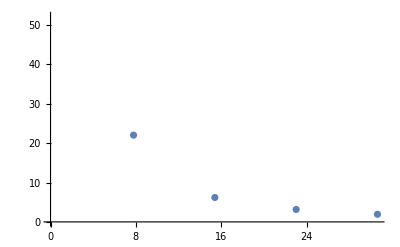

```mathematica
partacslpd=Multicolumn[Join[PartACsDetectorHeight,PartACsBGDTCorrectedCountRate],2]//First;
PartACsDataPlot=ListPlot[partacslpd]
```

{{12.0625,1.55936},{9.125,2.73304},{6.0625,5.93077},{3.0625,17.8164},{1.0625,77.8779}}

{{0.079375,10},{0.079375,10},{0.079375,10},{0.079375,10},{0.079375,10}}

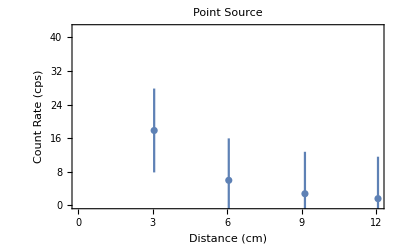

{0.079375,0.079375,0.079375,0.079375,0.079375}

Part::pkspec1: The expression i cannot be used as a part specification.

Table::iterb: Iterator {ErrorBar[{0.079375,0.079375,0.079375,0.079375,0.079375}⟦i⟧,{10,10,10,10,10}⟦i⟧]} does not have appropriate bounds.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Table::iterb: Iterator {ErrorBar[{{1,0.079375},{2,0.079375},{3,0.079375},{4,0.079375},{5,0.079375}}⟦i⟧,{{1,10},{2,10},{3,10},{4,10},{5,10}}⟦i⟧]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListPlot::lpn: Table[ErrorBarPlots`Private`handlePlusMinus[{Transpose[{Range[Length[«1»]],{12.0625,9.125,6.0625,3.0625,1.0625}}]⟦i⟧,Transpose[{Range[Length[«1»]],{1.55936,2.73304,5.93077,17.8164,77.8779}}]⟦i⟧}],{ErrorBar[{{1.,0.079375},{2.,0.079375},{3.,0.079375},{4.,0.079375},{5.,0.079375}}⟦i⟧,{{1.,10.},{2.,10.},{3.,10.},{4.,10.},{5.,10.}}⟦i⟧]},{ErrorBarPlots`Private`handlePlusMinus[{i,Length[Transpose[{Range[«1»],{«5»}}]]}]}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[Table[ErrorBarPlots`Private`handlePlusMinus[{Transpose[{Range[Length[{12.0625,9.125,6.0625,3.0625,1.0625}]],{12.0625,9.125,6.0625,3.0625,1.0625}}]⟦i⟧,Transpose[{Range[Length[{1.55936,2.73304,5.93077,17.8164,77.8779}]],{1.55936,2.73304,5.93077,17.8164,77.8779}}]⟦i⟧}],{ErrorBar[{{1,0.079375},{2,0.079375},{3,0.079375},{4,0.079375},{5,0.079375}}⟦i⟧,{{1,10},{2,10},{3,10},{4,10},{5,10}}⟦i⟧]},{ErrorBarPlots`Private`handlePlusMinus[{i,Length[Transpose[{Range[Length[{12.0625,9.125,6.0625,3.0625,1.0625}]],{12.0625,9.125,6.0625,3.0625,1.0625}}]]}]}],{},Method→{OptimizePlotMarkers→False}]

```mathematica
partacolpd=Multicolumn[Join[PartACoDetectorHeight,PartACoBGDTCorrectedCountRate],2]//First
partacolpderr=Table[{2.54/32.,10},{i,Length[partacolpd]}]
PartACoDataPlot=ErrorListPlot[Table[{partacolpd[[i]],ErrorBar[2.54/32.,partacolpderr[[i,2]]]},{i,1,Length[partacolpd]}],
Frame->True,
FrameLabel->{Style["Distance (cm)",18],Style["Count Rate (cps)",18]},
PlotLabel->Style["Point Source",24],
ImageSize->Full]
partacolpderr[[;;,1]]
DoPlot[partacolpd[[;;,1]],partacolpd[[;;,2]],partacolpderr[[;;,1]],partacolpderr[[;;,2]]]
```

6. From the plots created, determine at what distance, if ever, the detection efficiency can be described by equation 8.8 over equation 8.7 in the text with an error of no more than 5% for each source. Compare the two answers and discuss if they are different or not and whether they agree with our rule of thumb.

Note: use the best guess geometric efficiency equation based upon the inspection of the plot from question 6.

Line Source

1. Make a table for the line source data with the same information contained within the table for the point source analysis.

```mathematica
PartBDistance={2, 6, 10, 14, 18, 22, 26, 30, 34}*2.54 (* cm *);
PartBCounts = {48692, 16490, 7018, 3564, 1988, 1222, 795, 514, 332};
PartBTime=60 (* seconds *);
PartBCountRate=PartBCounts/PartBTime//N
```

```mathematica
PartBPlotData=Table[{PartBDistance[[i]],PartBCountRate[[i]]},{i,Length[PartBCounts]}]
```

{{5.08,811.533},{15.24,274.833},{25.4,116.967},{35.56,59.4},{45.72,33.1333},{55.88,20.3667},{66.04,13.25},{76.2,8.56667},{86.36,5.53333}}

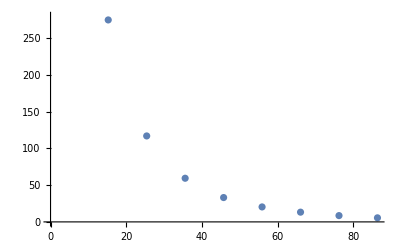

```mathematica
ListPlot[PartBPlotData]
```

2. Determine the total line energetic photon emission activity (E_γ≥30keV) with uncertainty. Assume the source strength of each source is known to ±5%.

3. Create a function that can be plotted that will provide the count rate versus distance for the line source data.

4. Plot the properly corrected count rate (with error bars) vs. distance. Interpolate between the data points with an interpolation order of 2. Also include the theoretical detection efficiency for both a line source and a 1/r^2 (point) source. Include a legend to identify which curve is which (i.e., data vs. calculated).

To make the theoretical detection efficiency viewable on the same plot, students should scale by the corresponding source energetic photon emission activity and estimate a constant intrinsic detection efficiency to get the two on the same order of magnitude (go with whatever value works).

5. From the plots created, determine at what distance, if ever, the detection efficiency can be described by equation 8.8 in the text vs. the appropriate line source equation with an error of no more than 5%. Does the result agree with our rule of thumb?

Area Source

1. Make a table for the square source data with the same information contained within the table for the point source analysis.

```mathematica
PartCDistance=List[6,9,12,15,18,21,24,27,30,33,36,39,42]*2.54 (* cm *);
PartCCounts={9385,5086,2927,1818,1167,767,550,1222,1000,775,655,506,480};
PartCTimes={60,60,60,60,60,60,60,200,200,200,200,200,200};
PartCCountRates=PartCCounts/PartCTimes//N
PartCDistanceError=0.25*2.54;
```

{156.417,84.7667,48.7833,30.3,19.45,12.7833,9.16667,6.11,5.,3.875,3.275,2.53,2.4}

```mathematica
y7uiok
```

2. Determine the total square energetic photon emission activity (E_γ≥30keV) with uncertainty. Assume the source strength of each source is known to ±5%.

3. Create a function that can be plotted that will provide the total count rate versus distance for the square source data.

4. Plot the properly corrected count rate (with error bars) vs. distance. Interpolate between the data point with an interpolation order of 2. Also include the theoretical detection efficiency for a square source and a 1/r^2 (point) source. Include a legend to identify which curve is which (i.e., data vs. calculated).

To make the theoretical detection efficiency viewable on the same plot, students should scale by the corresponding source energetic photon emission activity and estimate a constant intrinsic detection efficiency to get the two on the same order of magnitude (go with whatever value works).

5. From the plots created, determine at what distance, if ever, the detection efficiency can be described by equation 8.8 over equation 8.11 in the text with an error of no more than 5%. Does the result agree with our rule of thumb?